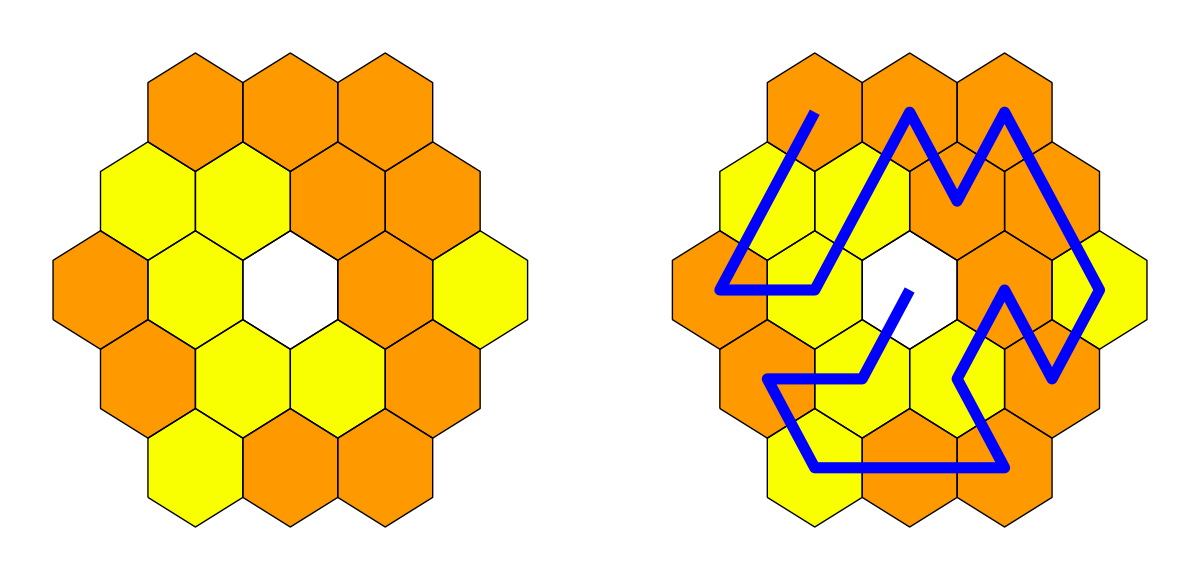

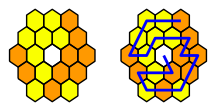

```mathematica
p[x_,y_]:={2Sqrt[3]/2 x-y Sqrt[3]/2,1.5y }
p[{x_,y_}]:=p[x,y]

board[nn_]:={Table[hex[i,j],{j,2,nn+1},{i,2,nn-1+j}],
	Table[hex[i,j],{j,nn+2,2nn},{i,j-nn+1,2nn}]}

hex[x_,y_]:={
	Line[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-Sqrt[3]/2,-1/2}}]}
```

```mathematica
colorhex[{x_,y_}]:=If[{x,y}=={(n+3)/2,(m+3)/2},{GrayLevel[1],
	Polygon[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1}}]},{Hue[A[[x,y]]],
	Polygon[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1}}]}]
```

```mathematica
box[nn_]:=Module[{},n=2 nn-1;m=2 nn-1;A=Table[If[i==1||i==n+2||j==1||j==m+2||Abs[i-j]≥nn,1,RandomInteger[{0,1}] 0.07+0.1],{i,n+2},{j,m+2}];chec[A,nn];If[Length[B]==1,pic1=Graphics[{colorhex/@Select[Flatten[Table[{i,j},{i,n+2},{j,m+2}],1],A⟦Sequence@@#1⟧<1&],board[nn]}];pic2=Graphics[{AbsoluteThickness[2],RGBColor[0,0,1],Line[(p[#1]&)/@B⟦1⟧]}];p1=Show[pic1,AspectRatio->Automatic,ImageSize->{15 (2 n-1),15 (2 n-1)}];p2=Show[{pic1,pic2},AspectRatio->Automatic,ImageSize->{15 (2 n-1),15 (2 n-1)},PlotRange->All];Print[p1];Print[p2]]]
```

```mathematica
chec[A_,nn_]:=Module[{},
		B={};
		stack={{{nn+1,nn+1}}};
    While[Length[stack]>0&&Length[B]<2,
			path=Last[stack];
			stack=Drop[stack,-1];
			last=Last[path];
posss={last+{1,0},last+{0,1},last+{-1,0},last+{0,-1},last+{1,1},last+{-1,-1}};
			nbrs=Select[posss,!MemberQ[path,#]&&A[[Apply[Sequence,#]]]<1&];
If[Length[path]>1,
			dl=path[[-2]]-last;
		nbrs=Map[last+#&,Select[Map[#-last&,nbrs],MemberQ[angle[dl,last],#]&]]];
stack=Join[stack,Map[Join[path,{#}]&,nbrs]];
If[Length[nbrs]==0,If[Length[path]==Length[Position[A,x_/;x<1]],AppendTo[B,path]]]]]
```

```mathematica
angle[{1,1},bb_]:=If[A[[Apply[Sequence,bb]]]==.17,{{-1,0},{-1,-1},{0,-1}},{{-1,-1},{1,0},{0,1}}]
angle[{1,0},bb_]:=If[A[[Apply[Sequence,bb]]]==.17,{{-1,0},{-1,-1},{0,1}},{{-1,0},{1,1},{0,-1}}]
angle[{0,-1},bb_]:=If[A[[Apply[Sequence,bb]]]==.17,{{-1,0},{1,1},{0,1}},{{-1,-1},{1,0},{0,1}}]
angle[{-1,-1},bb_]:=If[A[[Apply[Sequence,bb]]]==.17,{{1,0},{1,1},{0,1}},{{1,1},{-1,0},{0,-1}}]
angle[{-1,0},bb_]:=If[A[[Apply[Sequence,bb]]]==.17,{{1,0},{1,1},{0,-1}},{{1,0},{0,1},{-1,-1}}]
angle[{0,1},bb_]:=If[A[[Apply[Sequence,bb]]]==.17,{{1,0},{-1,-1},{0,-1}},{{-1,0},{1,1},{0,-1}}]
```

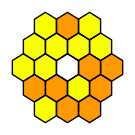

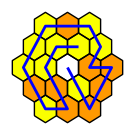

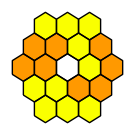

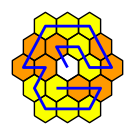

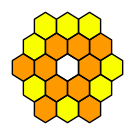

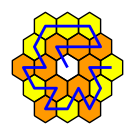

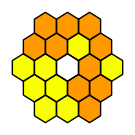

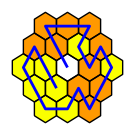

```mathematica
For[ll=1,ll<=100000,ll++,If[Mod[ll,10000]==0,Print[ll]];box[3]]
```

Start in the center, and draw a path that visits each hexagon exactly once. Your path can only turn gently (or go straight) in a yellow hexagon, and can only turn sharply (or go straight) in an orange hexagon.

## 3x3x3

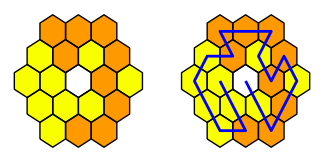

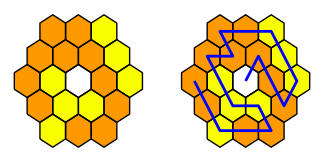

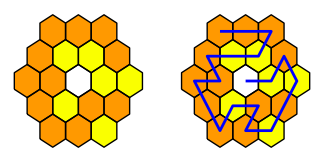

## 4x4x4